```mathematica
(*<<"/Users/wiese/Mathematica/libraries/Kay-initialization.m";
```

Directory for read/write is "/Users/wiese/Dropbox/tex/Kay/DLA/"

we look at corrections to g. There are two diagrams which have the same counting as a tree, and one which has an additional b. 
If we suppose that β(g)=ϵg-3g^2 for LERW, then for b-LRW we get β(g)=ϵg-(2+b)g^2.  
For d_f there is one diagram , proportional to b. This gives (we want to reproduce LERW) d_f=2-bg. The final result is
d_f=2-(b ϵ)/(2+b)

```mathematica
dfRG1L:=2-b ϵ/(2+b)
dfRG2L:=2-b ϵ/(2+b)-b (ϵ/(2+b))^2
dfSLE=1+3/(4(2b+1));
```

```mathematica
plotSLE=Plot[dfSLE,{b,0,10},PlotStyle->Red,PlotRange->All];
plotRG1L=Plot[dfRG1L/.ϵ->2,{b,0,10},PlotStyle->Cyan,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->2,{b,0,10},PlotStyle->Blue,PlotRange->All];
```

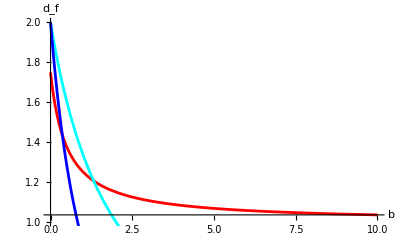

```mathematica
Show[{plotSLE,plotRG1L,plotRG2L},PlotRange->{1,2},AxesLabel->{b,Subscript[d, f]}]
```

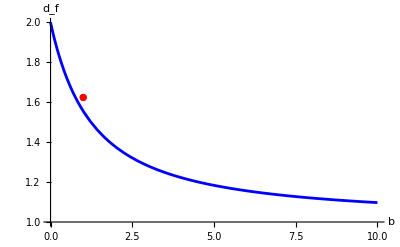

1.55556

d=3: error = -4.21456%

0.888889

error = -28.8889%

```mathematica
Plot[dfRG2L/.ϵ->1,{b,0,10},PlotStyle->Blue,PlotRange->{1,2}];
ListPlot[{{1,1.624}},PlotStyle->Red];
Show[%%,%,AxesLabel->{b,Subscript[d, f]}]
dfRG2L/.ϵ->1/.b->1.
Print["d=3: error = ",(%-1.624)/1.624*100,"%"]
dfRG2L/.ϵ->2/.b->1.
Print["error = ",(%-1.25)/1.25*100,"%"]
```

```mathematica
dfSLE/.b->0
```

7/4

```mathematica
1+κ/8/.κ->16/κ
%/.κ->2
```

1+2/κ

2